## Deriving Friedmann equations

```mathematica
$PrePrint=TraditionalForm;
(*Define coordinate system and FRW metric*)
coord={t,x,y,z};
metric=DiagonalMatrix[{-1,a[t]^2,a[t]^2,a[t]^2}]
<<"C:\\Users\\anugi\\OneDrive - King's College London\\Modern Computational Techniques for Theoretical Physicists\\diffgeo.m"
```

(-1 | 0 | 0 | 0
0 | (a(t))^2 | 0 | 0
0 | 0 | (a(t))^2 | 0
0 | 0 | 0 | (a(t))^2)

coord = {t,x,y,z}

ds2 = -𝕕[t]^2+a[t]^2 (𝕕[x]^2+𝕕[y]^2+𝕕[z]^2)

```mathematica
Einstein
```

((3 (a'(t))^2)/(a(t))^2 | 0 | 0 | 0
0 | -2 a(t) a''(t)-(a'(t))^2 | 0 | 0
0 | 0 | -2 a(t) a''(t)-(a'(t))^2 | 0
0 | 0 | 0 | -2 a(t) a''(t)-(a'(t))^2)

```mathematica
(*Define the energy-momentum tensor.*)
Subscript[T^μ, ν]=DiagonalMatrix[{-ρ,P,P,P}]
```

(-ρ | 0 | 0 | 0
0 | P | 0 | 0
0 | 0 | P | 0
0 | 0 | 0 | P)

```mathematica
RicciScalar
RicciTensor
metric
```

(6 (a(t) a''(t)+(a'(t))^2))/(a(t))^2

(-(3 a''(t))/(a(t)) | 0 | 0 | 0
0 | a(t) a''(t)+2 (a'(t))^2 | 0 | 0
0 | 0 | a(t) a''(t)+2 (a'(t))^2 | 0
0 | 0 | 0 | a(t) a''(t)+2 (a'(t))^2)

(-1 | 0 | 0 | 0
0 | (a(t))^2 | 0 | 0
0 | 0 | (a(t))^2 | 0
0 | 0 | 0 | (a(t))^2)

```mathematica
test1=RicciTensor-1/2 metric RicciScalar//Simplify
Einstein
```

((3 (a'(t))^2)/(a(t))^2 | 0 | 0 | 0
0 | -2 a(t) a''(t)-(a'(t))^2 | 0 | 0
0 | 0 | -2 a(t) a''(t)-(a'(t))^2 | 0
0 | 0 | 0 | -2 a(t) a''(t)-(a'(t))^2)

((3 (a'(t))^2)/(a(t))^2 | 0 | 0 | 0
0 | -2 a(t) a''(t)-(a'(t))^2 | 0 | 0
0 | 0 | -2 a(t) a''(t)-(a'(t))^2 | 0
0 | 0 | 0 | -2 a(t) a''(t)-(a'(t))^2)

```mathematica
(*Einstein's equations give us a system of equations which can be used to find equations of motion.*)
EinsteinEqs = Einstein == 8 π G metric Subscript[T^μ, ν]//Simplify
```

((3 (a'(t))^2)/(a(t))^2 | 0 | 0 | 0
0 | -2 a(t) a''(t)-(a'(t))^2 | 0 | 0
0 | 0 | -2 a(t) a''(t)-(a'(t))^2 | 0
0 | 0 | 0 | -2 a(t) a''(t)-(a'(t))^2)==(8 π G ρ | 0 | 0 | 0
0 | 8 π G P (a(t))^2 | 0 | 0
0 | 0 | 8 π G P (a(t))^2 | 0
0 | 0 | 0 | 8 π G P (a(t))^2)

```mathematica
(*For the Friedmann velocity equation, we need the 00 element of the matrix.*)
Friedmann1=EinsteinEqs[[1,1,1]]==EinsteinEqs[[2,1,1]]
(*For the acceleration equation, we need any of the other diagonal elements, and we can substitute for a'[t].*)
Friedmann2=Eliminate[{Friedmann1, EinsteinEqs[[1,2,2]]==EinsteinEqs[[2,2,2]]},a'[t]]//Simplify
```

(3 (a'(t))^2)/(a(t))^2==8 π G ρ

3 a''(t)+4 π G a(t) (3 P+ρ)==0

## The continuity equation

Conservation of the energy-momentum tensor gives us the continuity equation.

```mathematica
?covariant
```

```mathematica
(*To derive the continuity equation, take the zero component of the conservation equation.*)
(*Define the energy momentum tensor again, ensuring that ρ and P are in terms of t.*)
Subscript[T^μ, ν]= DiagonalMatrix[{-ρ[t],P[t],P[t],P[t]}];
covT = contract[covariant[metric Subscript[T^μ, ν]]]
continuityEq = covT[[1]]==0
```

{-(3 a'(t) (P(t)+ρ(t)))/(a(t))-ρ'(t),0,0,0}

-(3 a'(t) (P(t)+ρ(t)))/(a(t))-ρ'(t)==0

```mathematica
setP = {P[t]→ρ[t] w};
newContinuityEq = continuityEq/.setP;
rhoA = Integrate[continuityEq/.setP, t]
```

## Equations for inflaton

Run diffgeo first.

```mathematica
Clear[V];
Subscript[T^μ, ν]= DiagonalMatrix[{-ρ[t],P[t],P[t],P[t]}];

(*Substitute ρ and P for homogeneous scalar field.*)
scalarField = {ρ[t]->(1/2) (ϕ'[t])^2+V[ϕ[t]], P[t]->(1/2) (ϕ'[t])^2-V[ϕ[t]]};
EinsteinEqs = Einstein == 8 π G metric Subscript[T^μ, ν]/.scalarField//Simplify;

(*For the Friedmann velocity equation, we need the 00 element of the matrix.*)
Friedmann1=EinsteinEqs[[1,1,1]]==EinsteinEqs[[2,1,1]]
(*For the acceleration equation, we need any of the other diagonal elements, and we can substitute for a'[t].*)
Friedmann2=Eliminate[{Friedmann1, EinsteinEqs[[1,2,2]]==EinsteinEqs[[2,2,2]]},a'[t]]//Simplify
```

(3 (a'(t))^2)/(a(t))^2==4 π G (2 V(ϕ(t))+(ϕ'(t))^2)

8 π G a(t) (V(ϕ(t))-(ϕ'(t))^2)==3 a''(t)

```mathematica
(*Continuity equation for a scalar field.*)
covT = contract[covariant[metric Subscript[T^μ, ν]/.scalarField]];
continuityEq = covT[[1]]==0
```

-(3 a'(t) (ϕ'(t))^2)/(a(t))-ϕ'(t) (V'(ϕ(t))+ϕ''(t))==0

## Slow-roll approximation

```mathematica
(*Substitute a'[t]/a[t] with H[t]. We must explicitly substitute H^2=(a'[t]/a[t])^2.*)
conv = {a'[t]/a[t]->H[t],(a'[t]/a[t])^2->(H[t])^2};

(*Differentiate Friedmann velocity equation and eliminate V'[ϕ[t]] using the continuity equation.*)
diffH = D[Friedmann1/.conv,t];
HDot = Eliminate[{diffH, continuityEq/.conv},V'[ϕ[t]]]//Simplify
```

H(t) (4 π G (ϕ'(t))^2+H'(t))==0

## Single field inflation

```mathematica
Clear[V1];
(*Set G and mass.*)
sm = {G->1, m->1};

(*Applying slow-roll conditions.*)
V1[x_] := (1/2) m^2 (x)^2;
FEq = (a'[t]/a[t])^2==1/(3 Mpl^2) V1[ϕ[t]];
CEq = (3 a'[t] ϕ'[t])/a[t]+(V1'[ϕ[t]])==0;
(*Slow-roll conditions break down at ϵ=1 and η=1*)
epsn = Mpl^2/2 (V1'[ϕ[t]]/V1[ϕ[t]])^2==1;
eta = Mpl^2 V1''[ϕ[t]]/V1[ϕ[t]]==1; (*Note that this leads to the same equation as epsn.*)

(*Solve ϕ for when conditions break down.*)
ϕend=ϕ[t]/.Solve[epsn,ϕ[t]][[2]]

(*Solve number of e-folds N before break down for initial ϕ=ϕi*)
Nsol=(1/Mpl^2) Integrate[(V1[ϕ]/V1'[ϕ]),{ϕ,ϕend,ϕi}]//Simplify
```

√2 Mpl

1/4 (ϕi^2/Mpl^2-2)

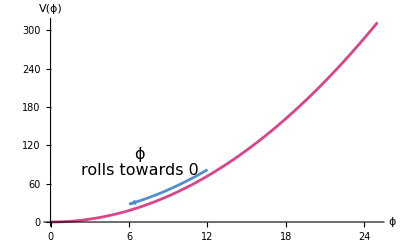

```mathematica
(*Set constants such that Subscript[M, pl] and m are 1.*)
setCons1 = {G->(1/(8 π)), m->1};

(*Plot potential.*)
p1 = Plot[V1[ϕ]/.setCons1,{ϕ,0,25},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All,AxesLabel->{ϕ,"V(ϕ)"}, LabelStyle->{FontSize->16, FontFamily->"Times", Black}];

(*Create label to show evolution of scalar field.*)
p2 = Plot[(V1[ϕ]+10)/.setCons1,{ϕ,6,12},PlotStyle->{RGBColor[0.32,0.56,0.81]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{-.05,0}], Arrow[x]};
t1 = Graphics[Text[Style[OverDot[ϕ,1], 16, FontFamily->"Times"], {6.8, 105}]];
t2 = Graphics[Text[Style["rolls towards 0", 16, FontFamily->"Times"], {6.8, 80}]];

Show[p1, p2, t1, t2]
```

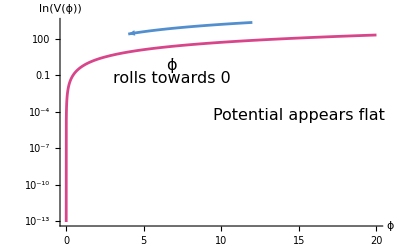

```mathematica
plot1 = LogPlot[V1[ϕ]/.setCons1,{ϕ,0,20},PlotStyle->{RGBColor[0.85,0.27,0.54]}, PlotRange->All,AxesLabel->{ϕ,"ln(V(ϕ))"}, LabelStyle->{FontSize->16, FontFamily->"Times", Black}, Ticks->None];
(*Create label to show evolution of scalar field.*)
plot2 = LogPlot[(V1[ϕ] 30)/.setCons1,{ϕ,4,12},PlotStyle->{RGBColor[0.32,0.56,0.81]}, PlotRange->All, Ticks->None]/. Line[x_] :> {Arrowheads[{-.05,0}], Arrow[x]};
text1 = Graphics[Text[Style[OverDot[ϕ,1], 16, FontFamily->"Times"], {6.8, -0.5}]];
text2 = Graphics[Text[Style["rolls towards 0", 16, FontFamily->"Times"], {6.8, -3}]];
text3 = Graphics[Text[Style["Potential appears flat", 16, FontFamily->"Times"], {15, -10}]];

Show[plot1, plot2, text1, text2, text3]
```

```mathematica
(*Set constants such that Subscript[M, pl] and m are 1.*)
setCons1 = {G->(1/(8 π)), m->1};

(*Substitute potential into equations of motion.*)
subPot = {V[ϕ[t]]->V1[ϕ[t]], V'[ϕ[t]]->V1'[ϕ[t]]};
eq1 = Friedmann1/.subPot/.setCons1
eq2 = continuityEq/.subPot/.setCons1

(*Use NDSolve to obtain numerical solutions for the Friedmann and continuity equations, as they are differential equations..*)
slns = NDSolve[{eq1, eq2, ϕ[0]==4, ϕ'[0]==-0.9, a[0]==1},{ϕ[t],a[t]},{t,0,500}]
```

(3 (a'(t))^2)/(a(t))^2==1/2 ((ϕ'(t))^2+(ϕ(t))^2)

-(3 a'(t) (ϕ'(t))^2)/(a(t))-ϕ'(t) (ϕ''(t)+ϕ(t))==0

NDSolve::ndsz: At t == 0.373441, step size is effectively zero; singularity or stiff system suspected.

{{ϕ(t)→InterpolatingFunction[…](t),a(t)→InterpolatingFunction[…](t)},{ϕ(t)→InterpolatingFunction[…](t),a(t)→InterpolatingFunction[…](t)}}

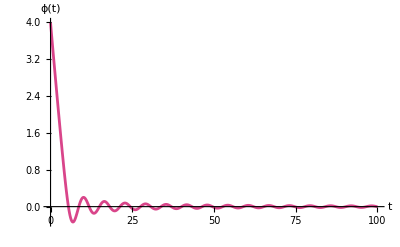

```mathematica
ϕsln[t_]:=ϕ[t]/.slns[[2]]
asln[t_]:=a[t]/.slns[[2]]

(*Plot solutions. Epilog is used to include inset of ϕ(t) for t=0 to t=5.*)
Plot[{ϕsln[t]},{t,0,100},PlotRange->All,AxesLabel->{t,"ϕ(t)"}, PlotStyle->{RGBColor[0.85,0.27,0.54]}, LabelStyle->{FontSize->16,FontFamily->"Times", Black}, Epilog->Inset[Plot[{ϕsln[t]}, {t,0,5}, PlotStyle->{RGBColor[0.85,0.27,0.54]}, ImageSize->190, Ticks->None, LabelStyle->{FontSize->14, FontFamily->"Times", Black}, Frame->True],{69, 2.7}]]
```

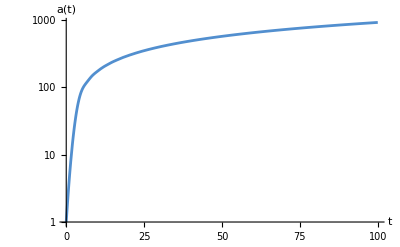

```mathematica
LogPlot[asln[t],{t,0,100},PlotRange->All,PlotStyle->{RGBColor[0.32,0.56,0.81]}, LabelStyle->{FontSize->20,FontFamily->"Times", ,Black}, AxesLabel->{t,"a(t)"}, Epilog->Inset[Plot[{asln[t]}, {t,0,6}, PlotStyle->{RGBColor[0.32,0.56,0.81]}, ImageSize->190, Ticks->None, LabelStyle->{FontSize->14, FontFamily->"Times", Black}, Frame->True],{69, 2.7}]]
```

```mathematica
(*Applying slow-roll conditions to Friedmann and continuity equations.*)
FEq = (a'[t]/a[t])^2==1/(3 Mpl^2) V1[ϕ[t]];
CEq = (3 a'[t] ϕ'[t])/a[t]+(V1'[ϕ[t]])==0;

(*Solve Friedmann and continuity equations to get ϕ[t] and a[t].*)
sol1 = DSolve[{FEq, CEq, ϕ[0]==ϕi, a[0]==ai},{ϕ[t],a[t]}, t]
```

{{ϕ(t)→1/3 (3 ϕi-√6 m Mpl t),a(t)→ai ⅇ^(1/6 m ((√6 t ϕi)/Mpl-m t^2))},{ϕ(t)→1/3 (√6 m Mpl t+3 ϕi),a(t)→ai ⅇ^(-(m (m Mpl t^2+√6 t ϕi))/(6 Mpl))}}

{Mpl→1,m→1,ϕi→4,ai→1}

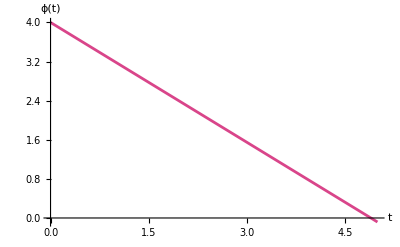

```mathematica
(*Set constants. ϕi must be larger than 3 Mpl.*)
setCons = {Mpl->1, m->1, ϕi->4, ai->1}

(*Plot ϕ[t] and a[t].*)
ϕsol[t_]:=ϕ[t]/.sol1[[1]]/.setCons
asol[t_]:=a[t]/.sol1[[1]]/.setCons
Plot[{ϕsol[t]},{t,0,5},PlotRange->All,AxesLabel->{t,"ϕ(t)"}, PlotStyle->{RGBColor[0.85,0.27,0.54]},LabelStyle->{FontSize->20,FontFamily->"Times", ,Black}]
```

```mathematica
(*Calculate time t that inflation ends*)
ϕ1[t_]:=ϕ[t]/.sol1[[1]]
inflTime = ϕ1[t]==ϕend
Solve[{inflTime,t}]
```

1/3 (3 ϕi-√6 m Mpl t)==√2 Mpl

{Solve (1/3 (3 ϕi-√6 m Mpl t)==√2 Mpl),Solve t}

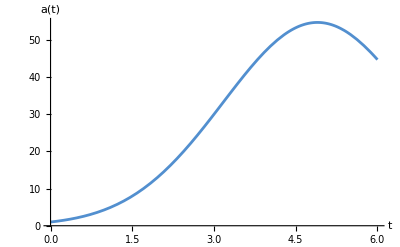

```mathematica
Plot[asol[t],{t,0,6},PlotRange->All,PlotStyle->{RGBColor[0.32,0.56,0.81]},LabelStyle->{FontSize->20,FontFamily->"Times", ,Black}, AxesLabel->{t,"a(t)"}]
```

1/6 ⅇ^(1/6 (23.2702 t-t^2)) (23.2702-2 t)

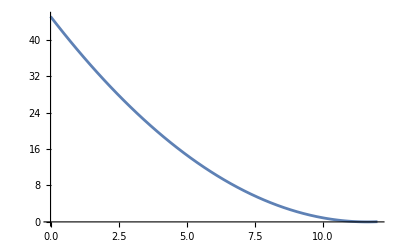

-Graphics-

```mathematica
Clear[aDash]
aDash=D[asol[t],t]
Plot[{1/2 ϕsol[t]^2},{t,0,12},PlotRange->All]
Plot[{3 (aDash/asol[t])^2},{t,0,12},PlotRange->All]
```

## Power-law inflation

```mathematica
(*Do not need the slow-roll approximation - can get exact solution.*)
VPL[x_]:=V0 Exp[-√(2/p) x/Mpl];

(*Slow-roll conditions break down at ϵ=1 and η=1*)
epsn = Mpl^2/2 (VPL'[ϕ[t]]/VPL[ϕ[t]])^2==1
eta = Mpl^2 VPL''[ϕ[t]]/VPL[ϕ[t]]==1 (*Note that this leads to the same equation as epsn.*)

(*Applying slow-roll conditions to Friedmann and continuity equations.*)
FEq2 = (a'[t]/a[t])^2==(1/(3 Mpl^2)) [VPL[ϕ[t]]+1/2 ϕ'[t]^2]
CEq2 = (3 a'[t] ϕ'[t])/a[t]+(VPL'[ϕ[t]])+ϕ''[t]==0

(*Solve Friedmann and continuity equations to get ϕ[t] and a[t].*)
sol2 = DSolve[{FEq2, CEq2, ϕ[0]==9.5, a[0]==a0},{ϕ[t],a[t]}, t]
```

1/p==1

2/p==1

(a'(t))^2/(a(t))^2==1/(3 Mpl^2)(V0 ⅇ^(-(√2 √(1/p) ϕ(t))/Mpl)+1/2 (ϕ'(t))^2)

(3 a'(t) ϕ'(t))/(a(t))-(√2 √(1/p) V0 ⅇ^(-(√2 √(1/p) ϕ(t))/Mpl))/Mpl+ϕ''(t)==0

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (NDSolve`ϕ$1)^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ϕ^ComplexInfinity encountered.

DSolve[{(a'(t))^2/(a(t))^2==1/(3 Mpl^2)(V0 ⅇ^(-(√2 √(1/p) ϕ(t))/Mpl)+1/2 (ϕ'(t))^2),(3 a'(t) ϕ'(t))/(a(t))-(√2 √(1/p) V0 ⅇ^(-(√2 √(1/p) ϕ(t))/Mpl))/Mpl+ϕ''(t)==0,ϕ(0)==9.5,a(0)==a0},{ϕ(t),a(t)},t]